```mathematica
InflationAdjust[Quantity[1,"USDollars"],DateObject[]]
```

1.00 $(USDollarsThu 23 Apr 2020)

```mathematica
InflationAdjust[Quantity[1,"USDollars"],DateObject[{1,1,1950}]]
```

InflationAdjust::datenc: USDollars unit can only be converted from 1774 to 2020.

Missing[NotAvailable]

```mathematica
InflationAdjust[Quantity[1,"USDollars"],DateObject[{1,1,1950},"Day"]]
```

InflationAdjust::datenc: USDollars unit can only be converted from 1774 to 2020.

Missing[NotAvailable]

```mathematica
InflationAdjust[Quantity[1,"USDollars"],DateObject[{1950,1,1}]]
```

0.09 $(USDollarsSun 1 Jan 1950)

```mathematica
InflationAdjust[Quantity[10,"USDollars"],DateObject[{1950,1,1}]]
```

0.91 $(USDollarsSun 1 Jan 1950)

```mathematica
InflationAdjust[Quantity[1000,"USDollars"],DateObject[{1950,1,1}]]
```

91.12 $(USDollarsSun 1 Jan 1950)

```mathematica
InflationAdjust[Quantity[1000000,"USDollars"],DateObject[{1950,1,1}]]
```

91 115.03 $(USDollarsSun 1 Jan 1950)

```mathematica
InflationAdjust[Quantity[1,DatedUnit["USDollars",1900]]]
```

32.28 $(USDollars2020)

```mathematica
InflationAdjust[Quantity[1,DatedUnit["USDollars",1950]]]
```

10.92 $(USDollars2020)

```mathematica
InflationAdjust[Quantity[1,"USDollars"],DateObject[{1950,1,1}]]
```

0.09 $(USDollarsSun 1 Jan 1950)

```mathematica
With[{apple=FinancialData["NASDAQ:AAPL","Close",All]},
Transpose[{
apple["Dates"],
apple["Values"]
}]
]
```

{{Fri 12 Dec 1980 00:00:00GMT-7.,0.51 $},{Mon 15 Dec 1980 00:00:00GMT-7.,0.49 $},{Tue 16 Dec 1980 00:00:00GMT-7.,0.45 $},{Wed 17 Dec 1980 00:00:00GMT-7.,0.46 $},{Thu 18 Dec 1980 00:00:00GMT-7.,0.48 $},9921,{Thu 16 Apr 2020 00:00:00GMT-7.,286.69 $},{Fri 17 Apr 2020 00:00:00GMT-7.,282.80 $},{Mon 20 Apr 2020 00:00:00GMT-7.,276.93 $},{Tue 21 Apr 2020 00:00:00GMT-7.,268.37 $},{Wed 22 Apr 2020 00:00:00GMT-7.,276.10 $}}
 |  |  |  |

```mathematica
data=Out[12]
```

{{Fri 12 Dec 1980 00:00:00GMT-7.,0.51 $},{Mon 15 Dec 1980 00:00:00GMT-7.,0.49 $},{Tue 16 Dec 1980 00:00:00GMT-7.,0.45 $},{Wed 17 Dec 1980 00:00:00GMT-7.,0.46 $},{Thu 18 Dec 1980 00:00:00GMT-7.,0.48 $},9921,{Thu 16 Apr 2020 00:00:00GMT-7.,286.69 $},{Fri 17 Apr 2020 00:00:00GMT-7.,282.80 $},{Mon 20 Apr 2020 00:00:00GMT-7.,276.93 $},{Tue 21 Apr 2020 00:00:00GMT-7.,268.37 $},{Wed 22 Apr 2020 00:00:00GMT-7.,276.10 $}}
 |  |  |  |

```mathematica
First@data
```

{Fri 12 Dec 1980 00:00:00GMT-7.,0.51 $}

```mathematica
InflationAdjust[
Quantity[.51,
DatedUnit["USDollars",DateObject[{1980,12,12,0,0,0.},"Instant","Gregorian",-7.]]]
,DateObject[{1950,1,1}]]
```

0.14 $(USDollarsSun 1 Jan 1950)

```mathematica
InflationAdjust[
Quantity[.51,"USDollars"]
,DateObject[{1950,1,1}]]
```

0.05 $(USDollarsSun 1 Jan 1950)

```mathematica
{First@#,InflationAdjust[
Quantity[Last@#,
DatedUnit["USDollars",DateObject[{1980,12,12,0,0,0.},"Instant","Gregorian",-7.]]]
,DateObject[{1950,1,1}]]}&/@data
```

{{Fri 12 Dec 1980 00:00:00GMT-7.,0.0129856 $^2(USDollarsSun 1 Jan 1950)},{Mon 15 Dec 1980 00:00:00GMT-7.,0.012308 $^2(USDollarsSun 1 Jan 1950)},{Tue 16 Dec 1980 00:00:00GMT-7.,0.0114047 $^2(USDollarsSun 1 Jan 1950)},9926,{Tue 21 Apr 2020 00:00:00GMT-7.,6.78795 $^2(USDollarsSun 1 Jan 1950)},{Wed 22 Apr 2020 00:00:00GMT-7.,6.98346 $^2(USDollarsSun 1 Jan 1950)}}
 |  |  |  |

```mathematica
{First@#,
InflationAdjust[
Quantity[
QuantityMagnitude@Last@#,
DatedUnit["USDollars",First@#]
]
,DateObject[{1950,1,1}]
]
}&/@data
```

{{Fri 12 Dec 1980 00:00:00GMT-7.,InflationAdjust[0.51 $(USDollarsFri 12 Dec 1980 00:00:00),{1950,1,1}]},{Mon 15 Dec 1980 00:00:00GMT-7.,InflationAdjust[0.49 $(USDollarsMon 15 Dec 1980 00:00:00),{1950,1,1}]},9928,{Wed 22 Apr 2020 00:00:00GMT-7.,InflationAdjust[276.10 $(USDollarsWed 22 Apr 2020 00:00:00),{1950,1,1}]}}
 |  |  |  |

```mathematica
InflationAdjust[
Quantity[
QuantityMagnitude@Last@#,
DatedUnit["USDollars",First@#]
]
,DateObject[{1950,1,1}]
]&/@data
```

{InflationAdjust[0.51 $(USDollarsFri 12 Dec 1980 00:00:00),{1950,1,1}],InflationAdjust[0.49 $(USDollarsMon 15 Dec 1980 00:00:00),{1950,1,1}],InflationAdjust[0.45 $(USDollarsTue 16 Dec 1980 00:00:00),{1950,1,1}],9925,InflationAdjust[276.93 $(USDollarsMon 20 Apr 2020 00:00:00),{1950,1,1}],InflationAdjust[268.37 $(USDollarsTue 21 Apr 2020 00:00:00),{1950,1,1}],InflationAdjust[276.10 $(USDollarsWed 22 Apr 2020 00:00:00),{1950,1,1}]}
 |  |  |  |

```mathematica
InflationAdjust[FinancialData["NASDAQ:AAPL","Close",All],DateObject[{1950,1,1}]]
```

TimeSeries[…]

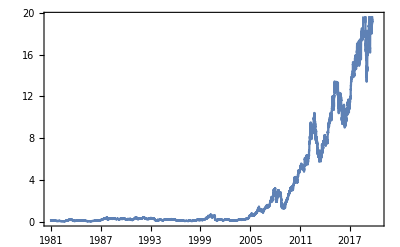

```mathematica
DateListPlot[Out[23]]
```

```mathematica
DateListPlot[{Out[23],FinancialData["NASDAQ:AAPL","Close",All]},
PlotRange->Full,PlotTheme->"Marketing",Joined->False,AspectRatio->1/3,ImageSize->Full]
```

-Graphics-

```mathematica
DateListPlot[{Out[23],FinancialData["NASDAQ:AAPL","Close",All]},
PlotRange->Full,PlotTheme->"Marketing",Joined->False,AspectRatio->1/3,ImageSize->Full,PlotLegends->{"Real",Nominal}]
```

-Graphics-

```mathematica
x^3+qx-r==0
```

qx-r+x^3==0

```mathematica
x^3+qx-r==0/.x->(u+v)
```

qx-r+(u+v)^3==0

```mathematica
ExpandAll[qx-r+(u+v)^3==0]
```

qx-r+u^3+3 u^2 v+3 u v^2+v^3==0